### Speed of a Quantum Walk

```mathematica
L=11;
```

```mathematica
M=Table[If[Abs[i-j]<= 1, If[i==j,0, 1], 0],{i, 1, L}, {j, 1, L}];
MatrixForm[M]
Val = Eigenvalues[M]//N;
Vec = Eigenvectors[Transpose[M]]//N;
Sol = Solve[Table[If[i==Ceiling[L/2], 1, 0], {i, 1, L}]==Sum[c[k] Vec[[k]], {k, 1, L}], Table[c[k], {k, 1, L}] ];
Coeff = Table[Sol[[1]][[i]][[2]], {i, 1, L}];
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

```mathematica
Psi[t_]:=Sum[Coeff[[k]] Vec[[k]] Exp[- I Val[[k]] t], {k, 1, L}]
Qprob[t_]:=Table[Abs[Psi[t][[k]]]^2, {k, 1, L}]
QprobAvg[t_]:= If[t==0, Qprob[0],(1/t)NIntegrate[Qprob[s], {s, 0, t}]]
```

```mathematica
Sum[QprobAvg[1][[k]], {k, 1, L}]
```

1.

```mathematica
plot =Flatten[Table[{k, t, QprobAvg[t][[k]]}, {k ,1, L}, {t, 0, 10, 1}],1];
```

```mathematica
ListPlot3D[plot, PlotRange->All]
```

-Graphics3D-

```mathematica
QEval[t_]:= Sum[k QprobAvg[t][[k]], {k, 1, L}];
```

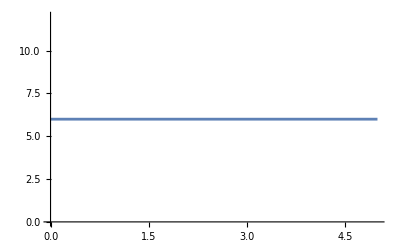

```mathematica
ListPlot[Table[{t, QEval[t]}, {t, 0, 5, 1}], Joined -> True]
```

```mathematica
Ceiling[L/2]
```

6

```mathematica
QSD[t_]:= (Sum[k^2 QprobAvg[t][[k]], {k, 1, L}] - Ceiling[L/2]^2)^(1/2);
```

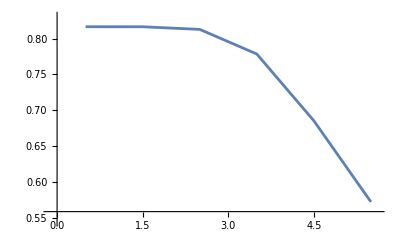

```mathematica
ListPlot[Table[{t, QSD[t]/t}, {t, 0.5, 5.5, 1}], Joined -> True]
```

```mathematica
N[√(2/3)]
```

0.816497

```mathematica
QSD[1/2]/(1/2)
```

0.816497

### Speed of a Quantum Walk

```mathematica
L=11;
J=2;
```

```mathematica
M=Table[If[Abs[i-j]<= 1, If[i==j,0, J], 0],{i, 1, L}, {j, 1, L}];
MatrixForm[M]
Val = Eigenvalues[M]//N;
Vec = Eigenvectors[Transpose[M]]//N;
Sol = Solve[Table[If[i==Ceiling[L/2], 1, 0], {i, 1, L}]==Sum[c[k] Vec[[k]], {k, 1, L}], Table[c[k], {k, 1, L}] ];
Coeff = Table[Sol[[1]][[i]][[2]], {i, 1, L}];
```

(0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0)

```mathematica
Psi[t_]:=Sum[Coeff[[k]] Vec[[k]] Exp[- I Val[[k]] t], {k, 1, L}]
Qprob[t_]:=Table[Abs[Psi[t][[k]]]^2, {k, 1, L}]
QprobAvg[t_]:= If[t==0, Qprob[0],(1/t)NIntegrate[Qprob[s], {s, 0, t}]]
```

```mathematica
Sum[QprobAvg[1][[k]], {k, 1, L}]
```

1.

```mathematica
plot =Flatten[Table[{k, t, QprobAvg[t][[k]]}, {k ,1, L}, {t, 0, 10, 1}],1];
```

```mathematica
ListPlot3D[plot, PlotRange->All]
```

-Graphics3D-

```mathematica
QEval[t_]:= Sum[k QprobAvg[t][[k]], {k, 1, L}];
```

```mathematica
ListPlot[Table[{t, QEval[t]}, {t, 0, 5, 1}], Joined -> True]
```

-Graphics-

```mathematica
Ceiling[L/2]
```

6

```mathematica
QSD[t_]:= (Sum[k^2 QprobAvg[t][[k]], {k, 1, L}] - Ceiling[L/2]^2)^(1/2);
```

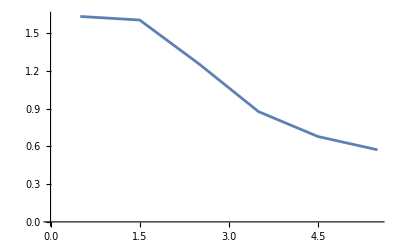

```mathematica
ListPlot[Table[{t, QSD[t]/t}, {t, 0.5, 5.5, 1}], Joined -> True]
```

```mathematica
N[J √(2 /3)]
```

1.63299

```mathematica
QSD[1/2]/(1/2)
```

1.63299

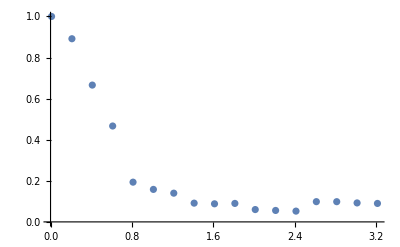

```mathematica
ListPlot[Table[{t, QprobAvg[t][[Floor[L/2]+Min[Ceiling[J t √(2/3)],Ceiling[L/2]]]]}, {t, 0.01, L/(2 J √(2/3)), 0.2}]]
```

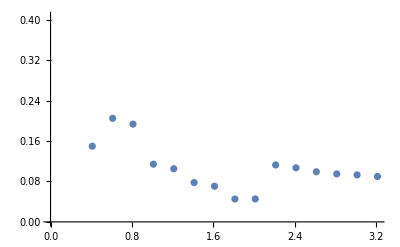

```mathematica
ListPlot[Table[{t, QprobAvg[t][[Floor[L/2]+Min[Ceiling[(1.5)J t √(2/3)],Ceiling[L/2]]]]}, {t, 0.01, L/(2 J √(2/3)), 0.2}]]
```

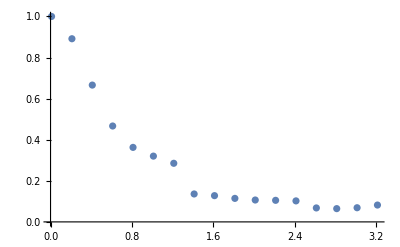

```mathematica
ListPlot[Table[{t, QprobAvg[t][[Floor[L/2]+Min[Ceiling[(0.5)J t √(2/3)],Ceiling[L/2]]]]}, {t, 0.01, L/(2 J √(2/3)), 0.2}]]
```

```mathematica
Floor[L/2]+Min[Ceiling[J t √(2/3)],Ceiling[L/2]]/. t->0.01
```

6

```mathematica
Ceiling[.1]
```

1

### Speed of a Quantum Walk

```mathematica
L=11;
J=1;
```

```mathematica
M=Table[If[Abs[i-j]<= 1, If[i==j,0, J], 0],{i, 1, L}, {j, 1, L}];
MatrixForm[M]
Val = Eigenvalues[M]//N;
Vec = Eigenvectors[Transpose[M]]//N;
Sol = Solve[Table[If[i==Ceiling[L/2], 1, 0], {i, 1, L}]==Sum[c[k] Vec[[k]], {k, 1, L}], Table[c[k], {k, 1, L}] ];
Coeff = Table[Sol[[1]][[i]][[2]], {i, 1, L}];
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

```mathematica
Psi[t_]:=Sum[Coeff[[k]] Vec[[k]] Exp[- I Val[[k]] t], {k, 1, L}]
Qprob[t_]:=Table[Abs[Psi[t][[k]]]^2, {k, 1, L}]
QprobAvg[t_, δ_]:= If[t==0, Qprob[0],Sum[Qprob[s], {s, 0, t, δ}]/Ceiling[t/δ]]
```

```mathematica
Sum[QprobAvg[1, π/10][[k]], {k, 1, L}]
```

1.

```mathematica
plot =Flatten[Table[{k, t, QprobAvg[t, π/10][[k]]}, {k ,1, L}, {t, 0, 50, 1}],1];
```

```mathematica
ListPlot3D[plot, PlotRange->All]
```

-Graphics3D-

```mathematica
QEval[t_]:= Sum[k QprobAvg[t, π/10][[k]], {k, 1, L}];
```

```mathematica
ListPlot[Table[{t, QEval[t]}, {t, 0, 5, 1}], Joined -> True]
```

-Graphics-

```mathematica
Ceiling[L/2]
```

6

```mathematica
QSD[t_]:= (Sum[k^2 QprobAvg[t, π/300][[k]], {k, 1, L}] - Ceiling[L/2]^2)^(1/2);
```

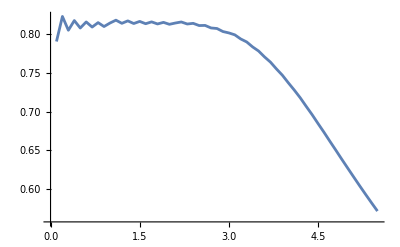

```mathematica
ListPlot[Table[{t, QSD[t]/t}, {t, 0.1, 5.5, .1}], Joined -> True]
```

```mathematica
N[J √(2 /3)]
```

0.816497

```mathematica
QSD[1/2]/(1/2)
```

0.78225

### Speed of a Quantum Walk

```mathematica
L=15;
J=10;
```

```mathematica
M =({{0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, J/2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, J/2, 0, J, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, J, 0, J, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, J, 0, J/2, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, J/2, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, J/2, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, J/2, 0, J, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, J, 0, J, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, J, 0, J/2, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, J/2, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}});
```

```mathematica
Val = Eigenvalues[M]//N;
Vec = Eigenvectors[Transpose[M]]//N;
Sol = Solve[Table[If[i==Ceiling[L/2], 1, 0], {i, 1, L}]==Sum[c[k] Vec[[k]], {k, 1, L}], Table[c[k], {k, 1, L}] ];
Coeff = Table[Sol[[1]][[i]][[2]], {i, 1, L}];
```

```mathematica
Psi[t_]:=Sum[Coeff[[k]] Vec[[k]] Exp[- I Val[[k]] t], {k, 1, L}]
Qprob[t_]:=Table[Abs[Psi[t][[k]]]^2, {k, 1, L}]
QprobAvg[t_, δ_]:= If[t==0, Qprob[0],Sum[Qprob[s], {s, 0, t, δ}]/Ceiling[t/δ]]
```

```mathematica
Sum[QprobAvg[1, π/10][[k]], {k, 1, L}]
```

1.

```mathematica
plot =Flatten[Table[{k, t, QprobAvg[t, π/10][[k]]}, {k ,1, L}, {t, 0, 10, 1}],1];
```

```mathematica
ListPlot3D[plot, PlotRange->All]
```

-Graphics3D-

```mathematica
QEval[t_]:= Sum[k QprobAvg[t, π/10][[k]], {k, 1, L}];
```

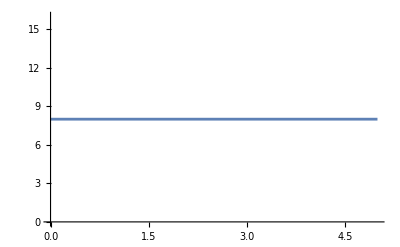

```mathematica
ListPlot[Table[{t, QEval[t]}, {t, 0, 5, 1}], Joined -> True]
```

```mathematica
Ceiling[L/2]
```

8

```mathematica
QSD[t_]:= (Sum[k^2 QprobAvg[t, π/300][[k]], {k, 1, L}] - Ceiling[L/2]^2)^(1/2);
```

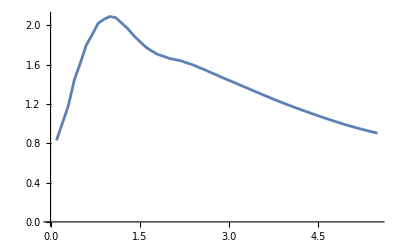

```mathematica
ListPlot[Table[{t, QSD[t]/t}, {t, 0.1, 5.5, .1}], Joined -> True]
```

```mathematica
N[J √(2 /3)]
```

0.816497

```mathematica
N[π/300]
```

0.010472

```mathematica
QSD[t_, δ_]:= (Sum[k^2 QprobAvg[t, δ][[k]], {k, 1, L}] - Ceiling[L/2]^2)^(1/2);
```

```mathematica
QSD[.01, .001 * π/300]/(.01)
```

0.816307

### Mixing time

```mathematica
Points={};
```

#### J =10

```mathematica
L=15;
J=10;
```

```mathematica
M =({{0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, J/2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, J/2, 0, J, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, J, 0, J, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, J, 0, J/2, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, J/2, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, J/2, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, J/2, 0, J, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, J, 0, J, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, J, 0, J/2, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, J/2, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}});
```

```mathematica
Val = Eigenvalues[M]//N;
DifVal = Flatten[Table[1/Abs[Val[[i]] - Val[[j]]], {i, 1, L-1}, {j, i+1, L}]];
AppendTo[Points,{J,Sum[DifVal[[k]], {k, 1, Length[DifVal]}]}]
```

{{10,594.564}}

#### J =15

```mathematica
L=15;
J=5;
```

```mathematica
M =({{0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, J/2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, J/2, 0, J, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, J, 0, J, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, J, 0, J/2, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, J/2, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, J/2, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, J/2, 0, J, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, J, 0, J, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, J, 0, J/2, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, J/2, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}});
```

```mathematica
Val = Eigenvalues[M]//N;
DifVal = Flatten[Table[1/Abs[Val[[i]] - Val[[j]]], {i, 1, L-1}, {j, i+1, L}]];
AppendTo[Points,{J,Sum[DifVal[[k]], {k, 1, Length[DifVal]}]}]
```

{{10,594.564},{5,319.222}}

#### J =20

```mathematica
L=15;
J=20;
```

```mathematica
M =({{0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, J/2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, J/2, 0, J, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, J, 0, J, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, J, 0, J/2, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, J/2, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, J/2, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, J/2, 0, J, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, J, 0, J, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, J, 0, J/2, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, J/2, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}});
```

```mathematica
Val = Eigenvalues[M]//N;
DifVal = Flatten[Table[1/Abs[Val[[i]] - Val[[j]]], {i, 1, L-1}, {j, i+1, L}]];
AppendTo[Points,{J,Sum[DifVal[[k]], {k, 1, Length[DifVal]}]}]
```

{{10,594.564},{5,319.222},{20,1152.31}}

#### J =7

```mathematica
L=15;
J=7;
```

```mathematica
M =({{0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, J/2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, J/2, 0, J, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, J, 0, J, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, J, 0, J/2, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, J/2, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, J/2, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, J/2, 0, J, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, J, 0, J, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, J, 0, J/2, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, J/2, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}});
```

```mathematica
Val = Eigenvalues[M]//N;
DifVal = Flatten[Table[1/Abs[Val[[i]] - Val[[j]]], {i, 1, L-1}, {j, i+1, L}]];
AppendTo[Points,{J,Sum[DifVal[[k]], {k, 1, Length[DifVal]}]}]
```

{{10,594.564},{5,319.222},{20,1152.31},{7,428.455}}

#### J =15

```mathematica
L=15;
J=15;
```

```mathematica
M =({{0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, J/2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, J/2, 0, J, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, J, 0, J, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, J, 0, J/2, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, J/2, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, J/2, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, J/2, 0, J, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, J, 0, J, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, J, 0, J/2, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, J/2, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}});
```

```mathematica
Val = Eigenvalues[M]//N;
DifVal = Flatten[Table[1/Abs[Val[[i]] - Val[[j]]], {i, 1, L-1}, {j, i+1, L}]];
AppendTo[Points,{J,Sum[DifVal[[k]], {k, 1, Length[DifVal]}]}]
```

{{10,594.564},{5,319.222},{20,1152.31},{7,428.455},{15,873.079}}

#### Fitting the points

```mathematica
Points = SortBy[Points, First]
```

{{5,319.222},{7,428.455},{10,594.564},{15,873.079},{20,1152.31}}

```mathematica
Points= {{5,319.22182050106665},{7,428.45476766037905},{10,594.5643658431453},{15,873.0794060011555},{20,1152.3066489980959}};
```

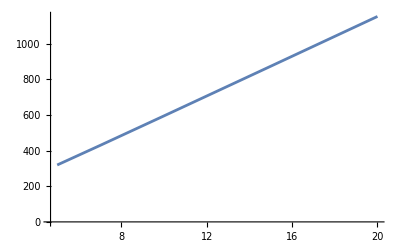

```mathematica
ListPlot[Points, Joined->True]
```

| Estimate | Standard Error | t-Statistic | P-Value
a1 | 39.9305 | 1.26567 | 31.549 | 0.0000699757
b1 | 55.5785 | 0.100122 | 555.105 | 1.28926×10^-8

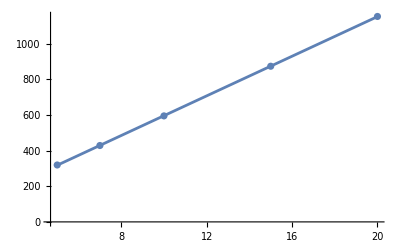

```mathematica
nlm1=NonlinearModelFit[Points,a1+b1 x,{a1,b1},x];
nlm1["ParameterTable"]
Show[ListPlot[Points],Plot[nlm1[x],{x,5,20}]]
```

### Limiting Distribution

We compare the distribution at the points 2, 5, 8, 11, 14 as a function of J.

```mathematica
Points2= {};
```

#### J=10

```mathematica
L=15;
J=10;
```

```mathematica
M =({{0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, J/2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, J/2, 0, J, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, J, 0, J, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, J, 0, J/2, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, J/2, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, J/2, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, J/2, 0, J, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, J, 0, J, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, J, 0, J/2, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, J/2, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}});
```

```mathematica
Val = Eigenvalues[M]//N;
Vec = Eigenvectors[Transpose[M]]//N;
Sol = Solve[Table[If[i==Ceiling[L/2], 1, 0], {i, 1, L}]==Sum[c[k] Vec[[k]], {k, 1, L}], Table[c[k], {k, 1, L}] ];
Coeff = Table[Sol[[1]][[i]][[2]], {i, 1, L}];
```

```mathematica
Psi[t_]:=Sum[Coeff[[k]] Vec[[k]] Exp[- I Val[[k]] t], {k, 1, L}]
Qprob[t_]:=Table[Abs[Psi[t][[k]]]^2, {k, 1, L}]
QprobAvg[t_, δ_]:= If[t==0, Qprob[0],Sum[Qprob[s], {s, 0, t, δ}]/Ceiling[t/δ]]
```

```mathematica
dist ={(QprobAvg[3 nlm1[J], π/10][[2]])/(QprobAvg[3 nlm1[J], π/10][[8]]), (QprobAvg[3 nlm1[J], π/10][[5]])/(QprobAvg[3 nlm1[J], π/10][[8]])}
```

{0.375301,0.0466836}

```mathematica
dist ={(QprobAvg[5 nlm1[J], π/10][[2]])/(QprobAvg[5 nlm1[J], π/10][[8]]), (QprobAvg[5 nlm1[J], π/10][[5]])/(QprobAvg[5 nlm1[J], π/10][[8]])}
```

{0.375445,0.0467261}

```mathematica
AppendTo[Points2,{J,dist[[2]]}]
```

{{10,0.0467261}}

#### J=5

```mathematica
L=15;
J=5;
```

```mathematica
M =({{0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, J/2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, J/2, 0, J, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, J, 0, J, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, J, 0, J/2, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, J/2, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, J/2, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, J/2, 0, J, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, J, 0, J, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, J, 0, J/2, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, J/2, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}});
```

```mathematica
Val = Eigenvalues[M]//N;
Vec = Eigenvectors[Transpose[M]]//N;
Sol = Solve[Table[If[i==Ceiling[L/2], 1, 0], {i, 1, L}]==Sum[c[k] Vec[[k]], {k, 1, L}], Table[c[k], {k, 1, L}] ];
Coeff = Table[Sol[[1]][[i]][[2]], {i, 1, L}];
```

```mathematica
Psi[t_]:=Sum[Coeff[[k]] Vec[[k]] Exp[- I Val[[k]] t], {k, 1, L}]
Qprob[t_]:=Table[Abs[Psi[t][[k]]]^2, {k, 1, L}]
QprobAvg[t_, δ_]:= If[t==0, Qprob[0],Sum[Qprob[s], {s, 0, t, δ}]/Ceiling[t/δ]]
```

```mathematica
dist ={(QprobAvg[3 nlm1[J], π/10][[2]])/(QprobAvg[3 nlm1[J], π/10][[8]]), (QprobAvg[3 nlm1[J], π/10][[5]])/(QprobAvg[3 nlm1[J], π/10][[8]])}
```

{0.421867,0.0572127}

```mathematica
dist ={(QprobAvg[5 nlm1[J], π/10][[2]])/(QprobAvg[5 nlm1[J], π/10][[8]]), (QprobAvg[5 nlm1[J], π/10][[5]])/(QprobAvg[5 nlm1[J], π/10][[8]])}
```

{0.421996,0.057264}

```mathematica
AppendTo[Points2,{J,dist[[2]]}]
```

{{10,0.0467261},{5,0.057264}}

#### J=20

```mathematica
L=15;
J=20;
```

```mathematica
M =({{0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, J/2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, J/2, 0, J, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, J, 0, J, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, J, 0, J/2, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, J/2, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, J/2, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, J/2, 0, J, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, J, 0, J, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, J, 0, J/2, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, J/2, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}});
```

```mathematica
Val = Eigenvalues[M]//N;
Vec = Eigenvectors[Transpose[M]]//N;
Sol = Solve[Table[If[i==Ceiling[L/2], 1, 0], {i, 1, L}]==Sum[c[k] Vec[[k]], {k, 1, L}], Table[c[k], {k, 1, L}] ];
Coeff = Table[Sol[[1]][[i]][[2]], {i, 1, L}];
```

```mathematica
Psi[t_]:=Sum[Coeff[[k]] Vec[[k]] Exp[- I Val[[k]] t], {k, 1, L}]
Qprob[t_]:=Table[Abs[Psi[t][[k]]]^2, {k, 1, L}]
QprobAvg[t_, δ_]:= If[t==0, Qprob[0],Sum[Qprob[s], {s, 0, t, δ}]/Ceiling[t/δ]]
```

```mathematica
dist ={(QprobAvg[3 nlm1[J], π/10][[2]])/(QprobAvg[3 nlm1[J], π/10][[8]]), (QprobAvg[3 nlm1[J], π/10][[5]])/(QprobAvg[3 nlm1[J], π/10][[8]])}
```

{0.363635,0.0440189}

```mathematica
dist ={(QprobAvg[5 nlm1[J], π/10][[2]])/(QprobAvg[5 nlm1[J], π/10][[8]]), (QprobAvg[5 nlm1[J], π/10][[5]])/(QprobAvg[5 nlm1[J], π/10][[8]])}
```

{0.363541,0.0440044}

```mathematica
AppendTo[Points2,{J,dist[[2]]}]
```

{{10,0.0467261},{5,0.057264},{20,0.0440044}}

#### J=7

```mathematica
L=15;
J=7;
```

```mathematica
M =({{0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, J/2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, J/2, 0, J, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, J, 0, J, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, J, 0, J/2, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, J/2, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, J/2, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, J/2, 0, J, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, J, 0, J, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, J, 0, J/2, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, J/2, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}});
```

```mathematica
Val = Eigenvalues[M]//N;
Vec = Eigenvectors[Transpose[M]]//N;
Sol = Solve[Table[If[i==Ceiling[L/2], 1, 0], {i, 1, L}]==Sum[c[k] Vec[[k]], {k, 1, L}], Table[c[k], {k, 1, L}] ];
Coeff = Table[Sol[[1]][[i]][[2]], {i, 1, L}];
```

```mathematica
Psi[t_]:=Sum[Coeff[[k]] Vec[[k]] Exp[- I Val[[k]] t], {k, 1, L}]
Qprob[t_]:=Table[Abs[Psi[t][[k]]]^2, {k, 1, L}]
QprobAvg[t_, δ_]:= If[t==0, Qprob[0],Sum[Qprob[s], {s, 0, t, δ}]/Ceiling[t/δ]]
```

```mathematica
dist ={(QprobAvg[3 nlm1[J], π/10][[2]])/(QprobAvg[3 nlm1[J], π/10][[8]]), (QprobAvg[3 nlm1[J], π/10][[5]])/(QprobAvg[3 nlm1[J], π/10][[8]])}
```

{0.391202,0.0504247}

```mathematica
dist ={(QprobAvg[5 nlm1[J], π/10][[2]])/(QprobAvg[5 nlm1[J], π/10][[8]]), (QprobAvg[5 nlm1[J], π/10][[5]])/(QprobAvg[5 nlm1[J], π/10][[8]])}
```

{0.392211,0.0504795}

```mathematica
AppendTo[Points2,{J,dist[[2]]}]
```

{{10,0.0467261},{5,0.057264},{20,0.0440044},{7,0.0504795}}

#### J=15

```mathematica
L=15;
J=15;
```

```mathematica
M =({{0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, J/2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, J/2, 0, J, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, J, 0, J, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, J, 0, J/2, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, J/2, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, J/2, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, J/2, 0, J, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, J, 0, J, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, J, 0, J/2, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, J/2, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}});
```

```mathematica
Val = Eigenvalues[M]//N;
Vec = Eigenvectors[Transpose[M]]//N;
Sol = Solve[Table[If[i==Ceiling[L/2], 1, 0], {i, 1, L}]==Sum[c[k] Vec[[k]], {k, 1, L}], Table[c[k], {k, 1, L}] ];
Coeff = Table[Sol[[1]][[i]][[2]], {i, 1, L}];
```

```mathematica
Psi[t_]:=Sum[Coeff[[k]] Vec[[k]] Exp[- I Val[[k]] t], {k, 1, L}]
Qprob[t_]:=Table[Abs[Psi[t][[k]]]^2, {k, 1, L}]
QprobAvg[t_, δ_]:= If[t==0, Qprob[0],Sum[Qprob[s], {s, 0, t, δ}]/Ceiling[t/δ]]
```

```mathematica
dist ={(QprobAvg[3 nlm1[J], π/10][[2]])/(QprobAvg[3 nlm1[J], π/10][[8]]), (QprobAvg[3 nlm1[J], π/10][[5]])/(QprobAvg[3 nlm1[J], π/10][[8]])}
```

{0.366817,0.0447263}

```mathematica
dist ={(QprobAvg[5 nlm1[J], π/10][[2]])/(QprobAvg[5 nlm1[J], π/10][[8]]), (QprobAvg[5 nlm1[J], π/10][[5]])/(QprobAvg[5 nlm1[J], π/10][[8]])}
```

{0.366234,0.0446752}

```mathematica
AppendTo[Points2,{J,dist[[2]]}]
```

{{10,0.0467261},{5,0.057264},{20,0.0440044},{7,0.0504795},{15,0.0446752}}

```mathematica
Points2 = SortBy[Points2, First]
```

{{5,0.057264},{7,0.0504795},{10,0.0467261},{15,0.0446752},{20,0.0440044}}

```mathematica
Points2= {{5,0.057263950510258385},{7,0.05047945114112996},{10,0.046726139460580206},{15,0.04467519244097728},{20,0.0440044347386029}};
```

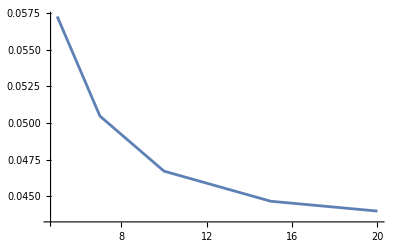

```mathematica
ListPlot[Points2, Joined->True]
```

| Estimate | Standard Error | t-Statistic | P-Value
a1 | -2.60347 | 0.0819324 | -31.7758 | 0.0000684913
b1 | -0.183726 | 0.034631 | -5.30524 | 0.0130743

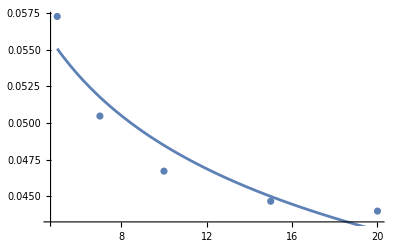

```mathematica
Ylog={Log[#[[1]]],Log[#[[2]]]}&/@Points2;
nlm1=NonlinearModelFit[Ylog,a1+b1 x,{a1,b1},x];
nlm1["ParameterTable"]
Show[ListPlot[Points2],Plot[Exp[nlm1[Log[x]]],{x,5,20}]]
```

| Estimate | Standard Error | t-Statistic | P-Value
a1 | -2.8511 | 0.0618568 | -46.092 | 0.0000224833
b1 | -0.0155443 | 0.00489327 | -3.17667 | 0.0502223

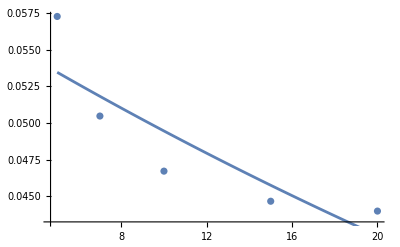

```mathematica
Ylog={#[[1]],Log[#[[2]]]}&/@Points2;
nlm1=NonlinearModelFit[Ylog,a1+b1 x,{a1,b1},x];
nlm1["ParameterTable"]
Show[ListPlot[Points2],Plot[Exp[nlm1[x]],{x,5,20}]]
```

```mathematica
(0.057263950510258385)^(-1/2)
```

4.17887

```mathematica
nlm1[5]
```

-2.92882

#### J=7

```mathematica
L=15;
J=2;
```

```mathematica
M =({{0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, J/2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, J/2, 0, J, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, J, 0, J, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, J, 0, J/2, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, J/2, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, J/2, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, J/2, 0, J, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, J, 0, J, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, J, 0, J/2, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, J/2, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}});
```

```mathematica
Val = Eigenvalues[M]//N;
Vec = Eigenvectors[Transpose[M]]//N;
Sol = Solve[Table[If[i==Ceiling[L/2], 1, 0], {i, 1, L}]==Sum[c[k] Vec[[k]], {k, 1, L}], Table[c[k], {k, 1, L}] ];
Coeff = Table[Sol[[1]][[i]][[2]], {i, 1, L}];
```

```mathematica
Psi[t_]:=Sum[Coeff[[k]] Vec[[k]] Exp[- I Val[[k]] t], {k, 1, L}]
Qprob[t_]:=Table[Abs[Psi[t][[k]]]^2, {k, 1, L}]
QprobAvg[t_, δ_]:= If[t==0, Qprob[0],Sum[Qprob[s], {s, 0, t, δ}]/Ceiling[t/δ]]
```

```mathematica
dist ={(QprobAvg[3 nlm1[J], π/10][[2]])/(QprobAvg[3 nlm1[J], π/10][[8]]), (QprobAvg[3 nlm1[J], π/10][[5]])/(QprobAvg[3 nlm1[J], π/10][[8]])}
```

{0.523865,0.0983134}

```mathematica
dist ={(QprobAvg[ nlm1[J]/4, π/10][[2]])/(QprobAvg[ nlm1[J]/4, π/10][[8]]), (QprobAvg[ nlm1[J]/4, π/10][[5]])/(QprobAvg[ nlm1[J]/4, π/10][[8]])}
```

{0.520395,0.0966037}

```mathematica
nlm1[J]
```

151.087

```mathematica
(0.1)^(-1/2)
```

3.16228

```mathematica
AppendTo[Points2,{J,dist[[2]]}]
```

{{10,0.0467261},{5,0.057264},{20,0.0440044},{7,0.0504795}}

```mathematica
8.95703 (3)^1.879
```

70.5789